```mathematica
ClearAll["Global`*"]
```

## Zigzag Periodic Impurity

```mathematica
ℏ=6.582*10^-1; (*meV/THz*)
```

### Hamiltonian

```mathematica
HamZZ[J_,Jp_,Da_,Db_,Ka_,Kb_,Z_,m_,M_]:=Module[{a,S},
(*Parameters*)
a=1;
S=1;
ϕ=If[Jp!=0,ArcTan[(Ca+Cb)/(2Jp)],π/2];
Ca=√(Da^2+Jp^2);
Cb=√(Db^2+Jp^2);
α1=-√3 a/2;
α2=√3 a/2;
β1=α1;
β2=α2;
β3=√3 a;

(*NN Terms*)
AB1[k_]:=N[-J S ⅇ^(ⅈ k  α1)];
AB2[k_]:=N[-J S ⅇ^(ⅈ (k) α2)];

(*NNN Terms*)
A1[k_]:=N[-Ca S ⅇ^(ⅈ (k β1+ϕ))];
A2[k_]:=N[-Ca S ⅇ^(ⅈ (k β2-ϕ))];
A3[k_]:=N[-Ca S ⅇ^(ⅈ (k β3+ϕ))];

B1[k_]:=N[-Cb S ⅇ^(ⅈ (k β1-ϕ))];
B2[k_]:=N[-Cb S ⅇ^(ⅈ (k β2+ϕ))];
B3[k_]:=N[-Cb S ⅇ^(ⅈ (k β3-ϕ))];



(*NN Matrix Elements*)
c1[k_]:=Table[{{4i-3,4i}->AB1[k],{4i,4i-3}->Conjugate[AB1[k]]},{i,1,m}];
c2[k_]:=Table[{{4i-3,4i-2}->AB2[k],{4i-2,4i-3}->Conjugate[AB2[k]]},{i,1,m}];
c3[k_]:=Table[{{4i-1,4i-2}->AB1[k],{4i-2,4i-1}->Conjugate[AB1[k]]},{i,1,m}];
c4[k_]:=Table[{{4i-1,4i}->AB2[k],{4i,4i-1}->Conjugate[AB2[k]]},{i,1,m}];
c5[k_]:=Table[{{4i-2,4i+1}->-J S ,{4i+1,4i-2}->-J S },{i,1,m-1}];
c6[k_]:=Table[{{4i,4i+3}->-J S ,{4i+3,4i}->-J S },{i,1,m-1}];

(*NNN Matrix Elements*)
d1[k_]:=Table[{{4i-3,4i+3}->A1[k],{4i+3,4i-3}->Conjugate[A1[k]]},{i,1,m-1}];
d2[k_]:=Table[{{4i-1,4i+1}->A1[k],{4i+1,4i-1}->Conjugate[A1[k]]},{i,1,m-1}];
d3[k_]:=Table[{{4i-2,4i+4}->B1[k],{4i+4,4i-2}->Conjugate[B1[k]]},{i,1,m-1}];
d4[k_]:=Table[{{4i,4i+2}->B1[k],{4i+2,4i}->Conjugate[B1[k]]},{i,1,m-1}];

d5[k_]:=Table[{{4i-3,4i-1}->(A3[k]+Conjugate[A3[k]]),{4i-1,4i-3}->(A3[k]+Conjugate[A3[k]])},{i,1,m}];
d6[k_]:=Table[{{4i-2,4i}->(B3[k]+Conjugate[B3[k]]),{4i,4i-2}->(B3[k]+Conjugate[B3[k]])},{i,1,m}];

d7[k_]:=Table[{{4i-3,4i+1}->A2[k],{4i+1,4i-3}->Conjugate[A2[k]]},{i,1,m-1}];
d8[k_]:=Table[{{4i-1,4i+3}->A2[k],{4i+3,4i-1}->Conjugate[A2[k]]},{i,1,m-1}];
d9[k_]:=Table[{{4i-2,4i+2}->B2[k],{4i+2,4i-2}->Conjugate[B2[k]]},{i,1,m-1}];
d10[k_]:=Table[{{4i,4i+4}->B2[k],{4i+4,4i}->Conjugate[B2[k]]},{i,1,m-1}];

(*Onsite Energies*)
e1=Table[{4i-3,4i-3}->3 J S+Z+2S Ka+6 Jp,{i,1,m}];
e2=Table[{4i-2,4i-2}->3 J S+Z+2S Kb+6 Jp,{i,1,m}];
e3=Table[{4i-1,4i-1}->3 J S+Z+2S Ka+6 Jp,{i,1,m}];
e4=Table[{4i,4i}->3 J S+Z+2 S Kb+6 Jp,{i,1,m}];

(*Hamiltonian w/ no impurities or onsite corrections*)
NoImp[k_]:=SparseArray[Flatten[{c1[k],c2[k],c3[k],c4[k],c5[k],c6[k],d1[k],d2[k],d3[k],d4[k],d5[k],d6[k],d7[k],d8[k],d9[k],d10[k],e1,e2,e3,e4}]];

(*Onsite Energy Edge Corrections*)
OS=SparseArray[{{1,1}->-J S-2 Jp S,{2,2}->-2 Jp S,{3,3}->-J S-2 Jp S,{4,4}->-2 Jp S,{-1,-1}->-J S-2 Jp S,{-3,-3}->-J S-2 Jp S,{-4,-4}->-2 Jp S,{-2,-2}->-2 Jp S},{4m,4m}];

(*Impurity corrections*)
Imp[k_]:=-SparseArray[{{4M-3,4M}->AB1[k],{4M,4M-3}->Conjugate[AB1[k]],{4M-1,4M}->AB2[k],{4M,4M-1}->Conjugate[AB2[k]],{4M,4M+3}->-J S ,{4M+3,4M}->-J S,{4M,4M+2}->B1[k],{4M+2,4M}->Conjugate[B1[k]],{4M-2,4M}->(B3[k]+Conjugate[B3[k]]),{4M,4M-2}->(B3[k]+Conjugate[B3[k]]),{4M,4M+4}->B2[k],{4M+4,4M}->Conjugate[B2[k]],{4M-4,4M}->B2[k],{4M-6,4M}->B1[k],{4M,4M-6}->Conjugate[B1[k]],{4M,4M-4}->Conjugate[B2[k]],{4M,4M}->3 J S+Z+2 S Kb+6 Jp,{4M-3,4M-3}->J S,{4M-1,4M-1}->J S,{4M+3,4M+3}->-J S,{4M+2,4M+2}->Jp S,{4M-2,4M-2}->2Jp S,{4M-4,4M-4}->Jp S,{4M+4,4M+4}->Jp S},{4m,4m}];

(*Full Hamiltonian*)
H[k_]:=NoImp[k]+Imp[k]+OS;


(*Eigensystem*)
Esys[k_]:=Eigensystem[Chop[N[H[k]]]];
eval[k_]:=N[Esys[k][[1]]];
evec[k_]:=N[Esys[k][[2]]];

]
```

```mathematica
Quiet[HamZZ[2,0.1,0.3,0.3,0.0,0,0.05,20,10]];
Clear[En];
En=ParallelMap[eval,Table[k,{k,-π/(2 √3),π/(2 √3),(2π)/2000}]];
```

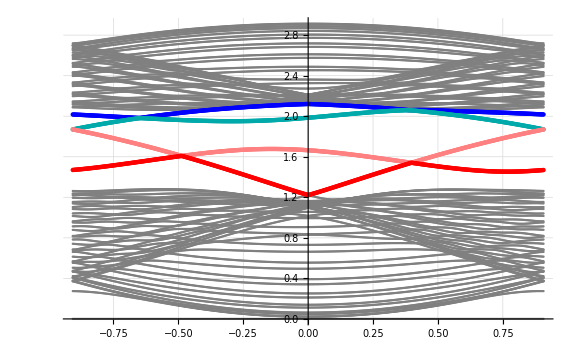

```mathematica
Show[ListPlot[Transpose[En]/(2Pi ℏ),PlotStyle->Gray,ImageSize->Large,DataRange->{-π/(2 √3),π/(2 √3)}],ListPlot[Transpose[En][[37]]/(2Pi ℏ),PlotStyle->Blue,ImageSize->Large,DataRange->{-π/(2 √3),π/(2 √3)}],
ListPlot[Transpose[En][[38]]/(2Pi ℏ),PlotStyle->Darker[Cyan],ImageSize->Large,DataRange->{-π/(2 √3),π/(2 √3)}],
ListPlot[Transpose[En][[39]]/(2Pi ℏ),PlotStyle->Pink,ImageSize->Large,DataRange->{-π/(2 √3),π/(2 √3)}],
ListPlot[Transpose[En][[40]]/(2Pi ℏ),PlotStyle->Red,ImageSize->Large,DataRange->{-π/(2 √3),π/(2 √3)}],GridLines->Automatic,PlotTheme->"Scientific"]
```

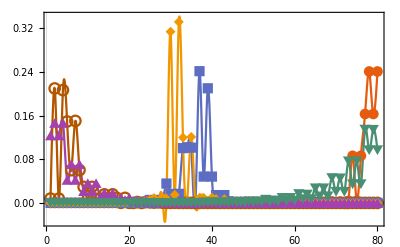

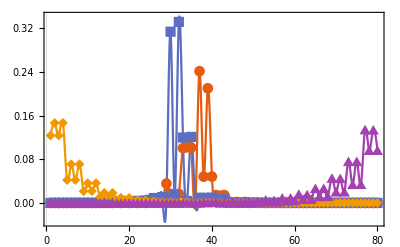

```mathematica
ka=0.1;
sortorder=Ordering[eval[ka]];
ListLinePlot[Table[(Abs[evec[ka][[sortorder]]]^2)[[j]],{j,41,46,1}],PlotRange->All,PlotMarkers->Automatic,InterpolationOrder->3,PlotTheme->"Scientific"]
ListLinePlot[Table[(Abs[evec[ka][[sortorder]]]^2)[[j]],{j,42,45,1}],PlotRange->All,PlotMarkers->Automatic,InterpolationOrder->3,PlotTheme->"Scientific"]
```

```mathematica
sortorder
```

{80,79,78,77,76,75,74,73,72,71,70,69,68,67,66,65,64,63,62,61,60,59,58,57,56,55,54,53,52,51,50,49,48,47,46,45,44,43,42,41,40,39,38,37,36,35,34,33,32,31,30,29,28,27,26,25,24,23,22,21,20,19,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}